# Tools for Complex

## Plots

```mathematica
ComplexPlot3D[Exp[z],{z,π},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
f[z_]:= Sin[z^2]/((1+z^2)^2)
g[z_]:= √(1+z^2)
ComplexPlot3D[f[z],{z,2},PlotLegends->Automatic]
ComplexPlot3D[g[z],{z,2},PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-

```mathematica
h[z_]:=√(z+ⅈ)
ComplexPlot3D[h[z],{z,2},PlotLegends->Automatic]
```

-Graphics3D-

## Parameterizations

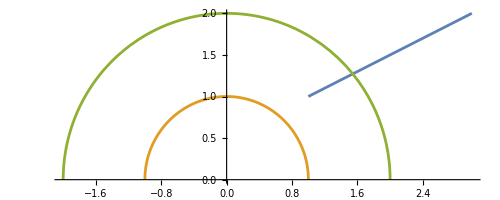

```mathematica
Clear[z1,z2,t,a,b]
z1[t_]:= 1+ⅈ + t (2 +ⅈ)
z2[t_]:= ⅇ^(π  ⅈ t)
z3[t_]:= 2 ⅇ^(π  ⅈ t^2)
ParametricPlot[{
ReIm[z1[t]],
ReIm[z2[t]],
ReIm[z3[t]]},{t,0, 1}]
```

## Mappings

### f(z)=z^2

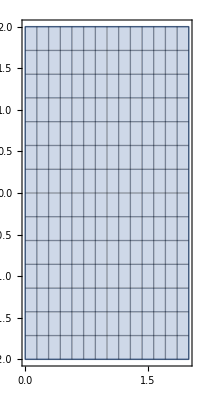
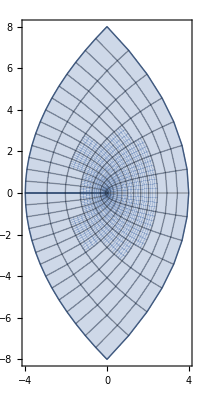
{-Graphics-,⟶,-Graphics-}

```mathematica
f[z_]:= z^2
{ParametricPlot[ReIm[x+ I y],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[x+ I y]],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All]}
```

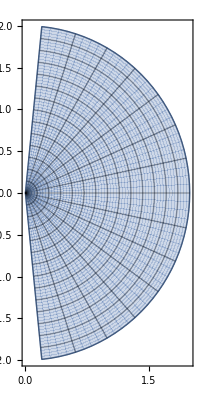
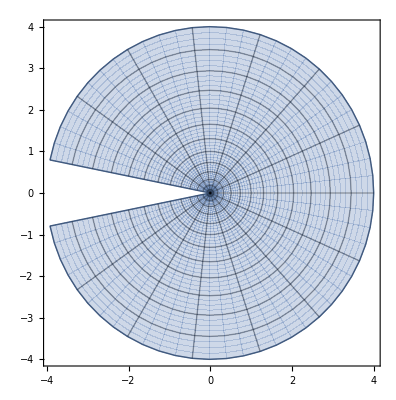
{-Graphics-,⟶,-Graphics-}

```mathematica
{ParametricPlot[ReIm[r ⅇ^(ⅈ θ)],{r,0,2},{θ,-π/2+0.1,π/2-0.1},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,0,2},{θ,-π/2+0.1,π/2-0.1},
Mesh->Full,
PlotRange->All]}
```

### f(z)=z^(1/2)

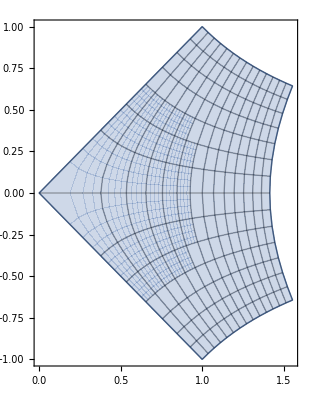
{-Graphics-,⟶,-Graphics-}

```mathematica
f[z_]:= z^(1/2)
{ParametricPlot[ReIm[x+ I y],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[x+ I y]],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All]}
```

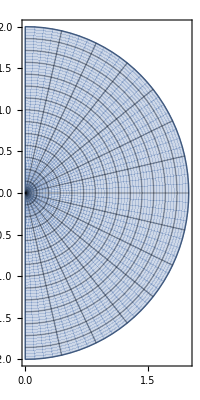
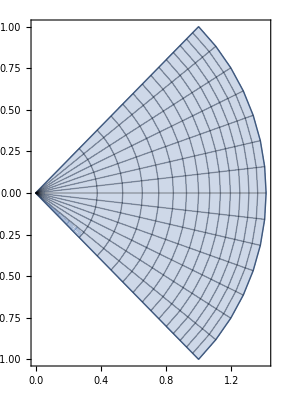
{-Graphics-,⟶,-Graphics-}

```mathematica
{ParametricPlot[ReIm[r ⅇ^(ⅈ θ)],{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
PlotRange->All]}
```

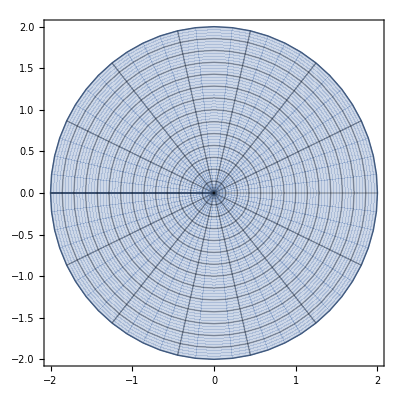
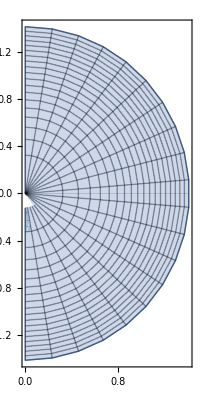
{-Graphics-,⟶,-Graphics-}

```mathematica
{ParametricPlot[ReIm[r ⅇ^(ⅈ θ)],{r,0,2},{θ,-π,π},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,0,2},{θ,-π,π},
Mesh->Full,
PlotPoints->20,
PlotRange->All]}
```

### f(z)=a z+ b

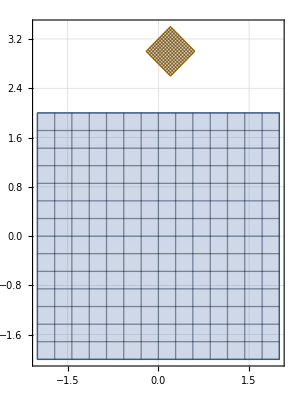

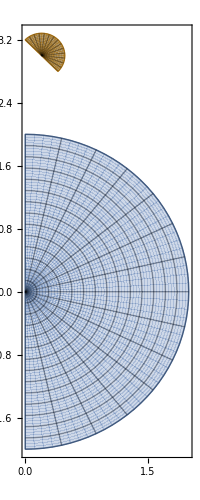

-Graphics3D-

```mathematica
a=0.1+0.1 ⅈ;
b=0.2+3ⅈ;
f[z_]:=a z + b 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,-2,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,10},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}
]
```

### f(z)=ⅇ^z

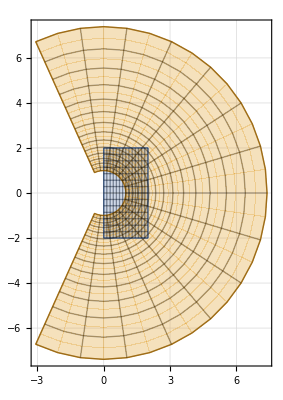

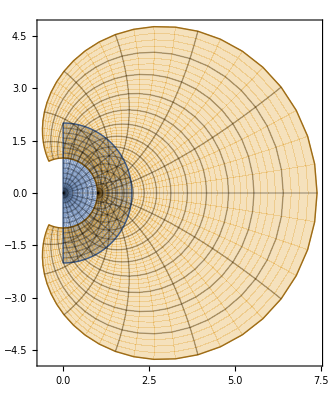

-Graphics3D-

```mathematica
f[z_]:=ⅇ^z 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=Log[z]

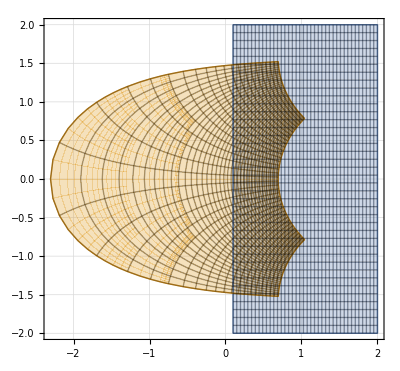

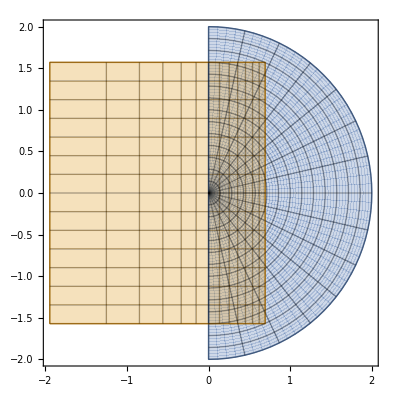

-Graphics3D-

```mathematica
f[z_]:=Log[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotPoints->40,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=Sin[z]

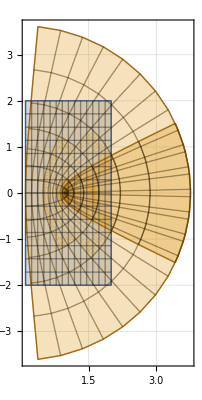

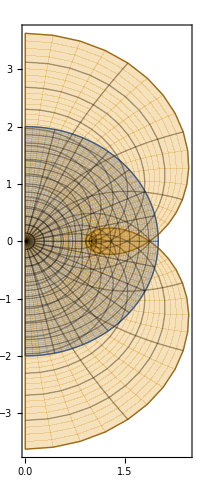

-Graphics3D-

```mathematica
f[z_]:=Sin[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=ArcSin[z]

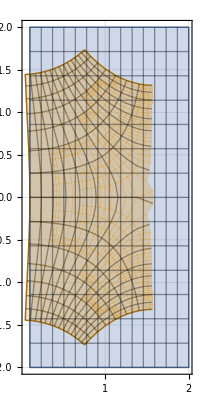

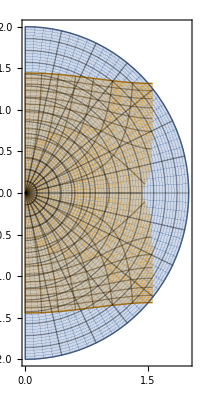

-Graphics3D-

```mathematica
f[z_]:=ArcSin[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=Tan[z]

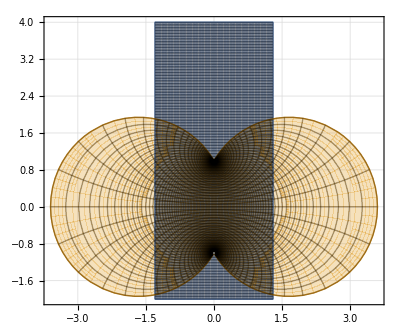

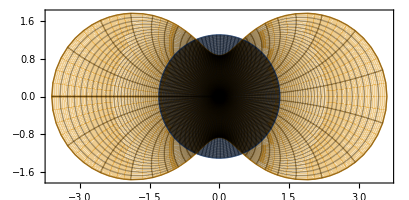

-Graphics3D-

```mathematica
f[z_]:=Tan[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,-1.3,1.3},{y,-2,4},
Mesh->Full,
PlotPoints->100,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,1.3},{θ,-π,π},
Mesh->Full,
PlotPoints->100,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,4},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=ArcTan[z]

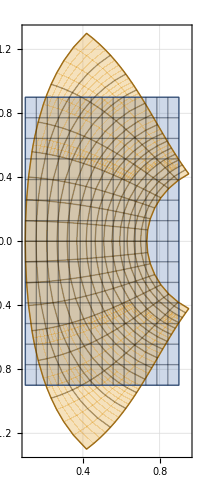

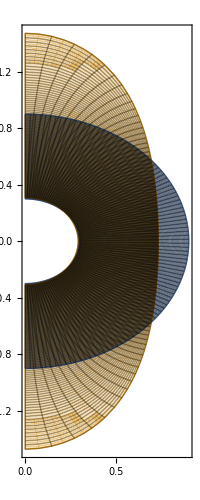

-Graphics3D-

{-Graphics3D-,-Graphics3D-}

```mathematica
f[z_]:=ArcTan[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,0.9},{y,-0.9,0.9},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0.3,0.9},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All,
PlotPoints->100]
ComplexPlot3D[f[z],{z,4},
PlotLegends->Automatic,
PlotRange->{0,2},
AxesLabel->{"re","im","Abs[f[z]]"}]

{ComplexPlot3D[z,{z,0.5},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}],
ComplexPlot3D[f[z],{z,0.5},
PlotLegends->Automatic,
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]}
```

```mathematica
R=0.8
{ComplexPlot3D[z,{z,R},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}],
ComplexPlot3D[f[z],{z,R},
PlotLegends->Automatic,
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]}
```

0.8

{-Graphics3D-,-Graphics3D-}

### f(z)=EulerPhi[z]

```mathematica
BesselJ[0, 1.0 + I]
```

0.937608-0.49653 ⅈ

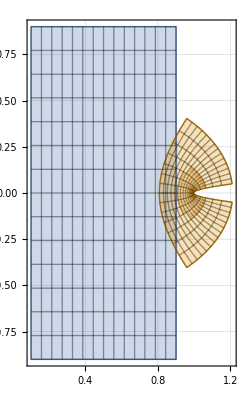

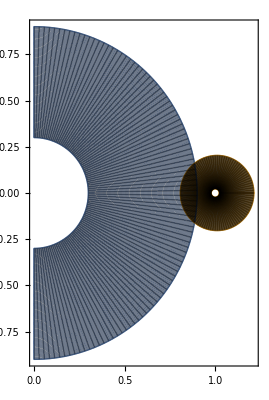

-Graphics3D-

```mathematica
f[z_]:=BesselJ[0,z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,0.9},{y,-0.9,0.9},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0.3,0.9},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All,
PlotPoints->100]
ComplexPlot3D[f[z],{z,4},
PlotLegends->Automatic,
PlotRange->{0,2},
AxesLabel->{"re","im","Abs[f[z]]"}]
```

## Branches

### z^(1/2)

We know that  z^(1/2) has two values.  Everybody decided (including computer programs) to chose the same principle branch!  Can we somehow plot more than one bit of the function. Can we pllot

```mathematica
f1[z_]:=z^(1/2)
R=2;
TabView[{
"CPlot3D"->ComplexPlot3D[ f1[z],{z, R},
PlotLegends->Automatic,
AxesLabel->{"re z","im z","abs(f1(z)"}],
"Abs"->ParametricPlot3D[{x,y, Abs[f1[x+ I y]]},
{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","abs(f1(z)"}],
"Arg"->ParametricPlot3D[{x,y, Arg[f1[x+ I y]]},
{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","arg(f1(z)"}]
}]
```

123

```mathematica
f2[z_]:=(-z)^(1/2)/ⅈ
R=2;
TabView[{
"CPlot3D"->ComplexPlot3D[ f2[z],{z, R},
PlotLegends->Automatic,
AxesLabel->{"re z","im z","abs(f2(z)"}],
"Abs"->ParametricPlot3D[{x,y, Abs[f2[x+ I y]]},
{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","abs(f2(z)"}],
"Arg"->ParametricPlot3D[{x,y, Arg[f2[x+ I y]]},
{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","arg(f2(z)"}]
}]
```

123

```mathematica
TabView[{
"Abs"->ParametricPlot3D[{
{x,y, Abs[f1[x+ I y]]},
{x,y, Abs[f2[x+ I y]]}
},
{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","abs(f(z)"}],
"Arg"->ParametricPlot3D[{
{x,y, Arg[f1[x+ I y]]},
{x,y, Arg[f2[x+ I y]]}
},
{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","arg(f(z)"}]}]
```

12

### √(1-z^2)

We know that  (1-z^2)^(1/2) has two values.  Everybody decided (including computer programs) to chose the same principle branch!  Can we somehow plot more than one bit of the function.  Could we find the other bits with plausible looking algebra.

```mathematica
f1[z_]:=(1-z^2)^(1/2)
R=2;
TabView[{
"CPlot3D"->ComplexPlot3D[ f1[z],{z, R},
PlotLegends->Automatic,
AxesLabel->{"re z","im z","abs(f1(z)"}],
"Abs"->ParametricPlot3D[{x,y, Abs[f1[x+ I y]]},
{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","abs(f1(z)"}],
"Arg"->ParametricPlot3D[{x,y, Arg[f1[x+ I y]]},
{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","arg(f1(z)"}]
}]
```

123

```mathematica
Series[ArcTan[x],{x,0,7}]
```

x-x^3/3+x^5/5-x^7/7+O[x]^8

## Power Series

In Calculus 2 you worked out power series for functions.  In complex analysis any nice function is defined (at least locally) by a power series.

### Bessel Js

```mathematica
f[z_]:=BesselJ[0,z]
Series[f[z],{z,0, 12}]
R=4;
TabView[{"CPlot"->ComplexPlot3D[f[z],{z,R},PlotLegends->Automatic,
AxesLabel->{"re z","im z","abs(f(z)"}],
"re"->ParametricPlot3D[{x,y,Re[f[x+I y]]},{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","re(f(z)"}],
"im"->ParametricPlot3D[{x,y,Im[f[x+I y]]},{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","im(f(z)"}],
"abs"->ParametricPlot3D[{x,y,Abs[f[x+I y]]},{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","abs(f(z)"}],
"arg"->ParametricPlot3D[{x,y,Arg[f[x+I y]]},{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","arg(f(z)"}]
}]
```

1-z^2/4+z^4/64-z^6/2304+z^8/147456-z^10/14745600+z^12/2123366400+O[z]^13

12345

### Sparse series! ∑_(k=0)^∞ z^(k^2)

```mathematica
f[z_]:=Sum[z^(j^2),{j,0, 5}]
Series[f[z],{z,0, 100}]
R=0.7;
TabView[{"CPlot"->ComplexPlot3D[f[z],{z,R},PlotLegends->Automatic,
AxesLabel->{"re z","im z","abs(f(z)"}],
"re"->ParametricPlot3D[{x,y,Re[f[x+I y]]},{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","re(f(z)"}],
"im"->ParametricPlot3D[{x,y,Im[f[x+I y]]},{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","im(f(z)"}],
"abs"->ParametricPlot3D[{x,y,Abs[f[x+I y]]},{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","abs(f(z)"}],
"arg"->ParametricPlot3D[{x,y,Arg[f[x+I y]]},{x,-R,R},{y,-R,R},
AxesLabel->{"re z","im z","arg(f(z)"}]
}]
```

1+z+z^4+z^9+z^16+z^25+O[z]^101

12345

```mathematica
f[z_]:=Sum[z^(j^2),{j,0, 5}]
Series[f[z],{z,0, 100}]
R=0.9;
TabView[{
"re"->ParametricPlot3D[{r Cos[θ],r Sin[θ],Re[f[r (Cos[θ]+ⅈ Sin[θ])]]},{r,0,R},{θ,-π,π},
AxesLabel->{"re z","im z","re(f(z)"}],
"im"->ParametricPlot3D[{r Cos[θ],r Sin[θ],Im[f[r (Cos[θ]+ⅈ Sin[θ])]]},{r,0,R},{θ,-π,π},
AxesLabel->{"re z","im z","im(f(z)"}],
"abs"->ParametricPlot3D[{r Cos[θ],r Sin[θ],Abs[f[r (Cos[θ]+ⅈ Sin[θ])]]},{r,0,R},{θ,-π,π},
AxesLabel->{"re z","im z","abs(f(z)"}],
"arg"->ParametricPlot3D[{r Cos[θ],r Sin[θ],Arg[f[r (Cos[θ]+ⅈ Sin[θ])]]},{r,0,R},{θ,-π,π},
AxesLabel->{"re z","im z","arg(f(z)"}]
}]
```

1+z+z^4+z^9+z^16+z^25+O[z]^101

1234

## Complex Conjugates

### Example 1

```mathematica
f[z_]:= z^3+ 1/(z+3 I+1)
ComplexExpand[f[x+ ⅈ y]];
u[x_,y_]:=x^3-3 x y^2+1/((1+x)^2+(3+y)^2)+x/((1+x)^2+(3+y)^2)
v[x_,y_]:= (3 x^2 y-y^3-3/((1+x)^2+(3+y)^2)-y/((1+x)^2+(3+y)^2))
uPic=ContourPlot[u[x,y],{x,-2,2},{y,-2,2},
ContourStyle->Blue,
Contours->20,
ContourShading->None];
vPic=ContourPlot[v[x,y],{x,-2,2},{y,-2,2},
ContourStyle->Red,
Contours->20,
ContourShading->None];
TabView[{
"u"->uPic,
"v"->vPic,
"u and v"->Show[uPic, vPic]
}]
```

123

### Example 2

```mathematica
f[z_]:= z^2+ z 
ComplexExpand[f[x+ ⅈ y]]
u[x_,y_]:=x+x^2-y^2
v[x_,y_]:= 2 x y +y
uPic=ContourPlot[u[x,y],{x,-2,2},{y,-2,2},
ContourStyle->Blue,
Contours->20,
ContourShading->None];
vPic=ContourPlot[v[x,y],{x,-2,2},{y,-2,2},
ContourStyle->Red,
Contours->20,
ContourShading->None];
TabView[{
"u"->uPic,
"v"->vPic,
"u and v"->Show[uPic, vPic]
},3]
```

x+x^2-y^2+ⅈ (y+2 x y)

123

## Exponential, Logs, z^w=exp(w log(z))

Well
a=ⅈ^ⅈ=exp(ⅈ log(ⅈ))=exp(ⅈ (ⅈ π/2 + ⅈ 2 k π))=exp(-(π/2+2πk))

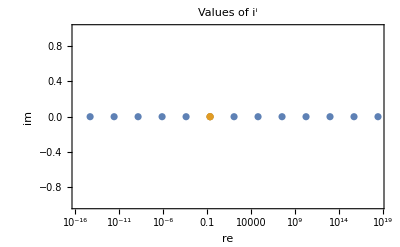

```mathematica
ListLogLinearPlot[ {
ReIm[Table[Exp[-0.5 π + 2 π k],{k,-5,7}]],
{{Exp[-0.5 π],0}}
},PlotRange->All,
GridLines->Automatic,Frame->True,FrameLabel->{"re","im"},
PlotLabel->"Values of i^i"]
```

Well
b=(1+ⅈ)^ⅈ

```mathematica
N[(1+ⅈ)^ⅈ]
```

0.428829+0.154872 ⅈ

```mathematica
Clear[f,z]
{xMin,xMax}={-10,3};
{yMin,yMax}={-0.9Pi,0.9Pi};
{rMin,rMax}={1,2};
{θMin,θMax}={π/2, 2π};
f[z_]:=Exp[z]
TabView[{
"x-y"->ParametricPlot[ReIm[x+ ⅈ y],{x,xMin,xMax},{y,yMin,yMax},
Mesh->All],
"Exp[x + I y]"->ParametricPlot[ReIm[f[x+ ⅈ y]],{x,xMin,xMax},{y,yMin,yMax},
Mesh->All],
"rⅇ^(ⅈ θ)"->ParametricPlot[ReIm[r E^(ⅈ θ)],{r,rMin,rMax},{θ,θMin,θMax},
Mesh->All],
"f[rⅇ^(ⅈ θ)]"->ParametricPlot[ReIm[f[r E^(ⅈ θ)]],{r,rMin,rMax},{θ,θMin,θMax},
Mesh->All,
PlotRange->All]
},3]
```

1234

```mathematica
Clear[f,z]
{xMin,xMax}={1,3};
{yMin,yMax}={0,2};
{rMin,rMax}={1,2};
{θMin,θMax}={π/2, 2π};
f[z_]:=z^z
TabView[{
"x-y"->ParametricPlot[ReIm[x+ ⅈ y],{x,xMin,xMax},{y,yMin,yMax},
Mesh->All],
"Exp[x + I y]"->ParametricPlot[ReIm[f[x+ ⅈ y]],{x,xMin,xMax},{y,yMin,yMax},
Mesh->All,
PlotRange->All],
"rⅇ^(ⅈ θ)"->ParametricPlot[ReIm[r E^(ⅈ θ)],{r,rMin,rMax},{θ,θMin,θMax},
Mesh->All],
"f[rⅇ^(ⅈ θ)]"->ParametricPlot[ReIm[f[r E^(ⅈ θ)]],{r,rMin,rMax},{θ,θMin,θMax},
Mesh->All,
PlotRange->All]
},2]
```

1234

```mathematica
Clear[f,z]
{xMin,xMax}={1,3};
{yMin,yMax}={0,2};
{rMin,rMax}={1,2};
{θMin,θMax}={π/2, π};
f[z_]:=z^ⅈ
TabView[{
"x-y"->ParametricPlot[ReIm[x+ ⅈ y],{x,xMin,xMax},{y,yMin,yMax},
Mesh->All],
"Exp[x + I y]"->ParametricPlot[ReIm[f[x+ ⅈ y]],{x,xMin,xMax},{y,yMin,yMax},
Mesh->All,
PlotRange->All],
"rⅇ^(ⅈ θ)"->ParametricPlot[ReIm[r E^(ⅈ θ)],{r,rMin,rMax},{θ,θMin,θMax},
Mesh->All],
"f[rⅇ^(ⅈ θ)]"->ParametricPlot[ReIm[f[r E^(ⅈ θ)]],{r,rMin,rMax},{θ,θMin,θMax},
Mesh->All,
PlotRange->All]
},2]
```

1234

```mathematica
Clear[f,z]
{xMin,xMax}={1,3};
{yMin,yMax}={0,2};
{rMin,rMax}={1,2};
{θMin,θMax}={π/2, π};
f[z_]:=(1+ⅈ)^z
TabView[{
"x-y"->ParametricPlot[ReIm[x+ ⅈ y],{x,xMin,xMax},{y,yMin,yMax},
Mesh->All],
"Exp[x + I y]"->ParametricPlot[ReIm[f[x+ ⅈ y]],{x,xMin,xMax},{y,yMin,yMax},
Mesh->All,
PlotRange->All],
"rⅇ^(ⅈ θ)"->ParametricPlot[ReIm[r E^(ⅈ θ)],{r,rMin,rMax},{θ,θMin,θMax},
Mesh->All],
"f[rⅇ^(ⅈ θ)]"->ParametricPlot[ReIm[f[r E^(ⅈ θ)]],{r,rMin,rMax},{θ,θMin,θMax},
Mesh->All,
PlotRange->All]
},2]
```

1234

## Complex Velocity Potential: Not done yet!

An analytic function f(z)=u(x,y)+ i v(x,y) describes a “flow field” with velocity V={p(x,y),q(x,y)} where p(x,y)=u(x,y) and q(x,y)=-v(x,y).  Note the minus sign!

Not done yet

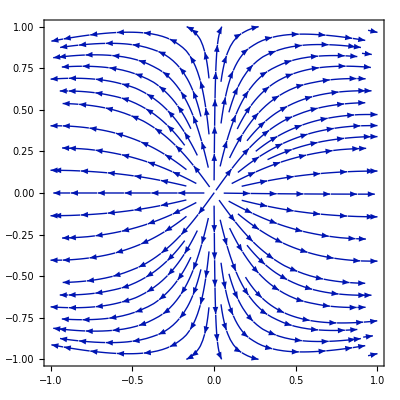

```mathematica
U=0.3;
m= 1.2-ⅈ;
a=1.1;
f[z_]:= U*(z+ a^2/z)
V[x_,y_]:= {Re[f[x+ I y]],-Im[f[x+ I y]]}
StreamPlot[V[x,y],{x,-1,1},{y,-1,1}]
```

Tat

## Taylor and Laurent Series

```mathematica
Series[f[z],{z,0,10}]
Series[f[1/u],{u,0,10}]
```

-1/z-1-z-z^2-z^3-z^4-z^5-z^6-z^7-z^8-z^9-z^10+O[z]^11

u^2+u^3+u^4+u^5+u^6+u^7+u^8+u^9+u^10+O[u]^11

```mathematica
f[z_]:=1/z(1/(z-1))
L1[z_,nMax_]:=-1/z- Sum[z^n,{n,0,nMax}]
L2[z_,nMax_]:= Sum[z^-n,{n,2,nMax}]
ϵ=0.1; nMax=4;
SetOptions[ComplexPlot, MaxRecursion->3];
TabView[
{"f"->ComplexPlot3D[f[z],{z,3},PlotRange->{0,10}],
"L1"->ComplexPlot3D[L1[z,nMax],{z,3},RegionFunction->Function[z,ϵ<Abs[z]<1-ϵ]],
"L2"->ComplexPlot3D[L2[z,nMax],{z,3},RegionFunction->Function[z,Abs[z]>1+ϵ]],
"f-L1"->ComplexPlot3D[f[z]-L1[z,nMax],{z,1},RegionFunction->Function[z,ϵ<Abs[z]<1-ϵ]],
"f-L2"->ComplexPlot3D[f[z]-L2[z,nMax],{z,3},RegionFunction->Function[z,Abs[z]>1+ϵ]]
}]
```

12345

```mathematica
12345
```

```mathematica
12345
```

## Contour Integrals

## Easy Conformal Mappings

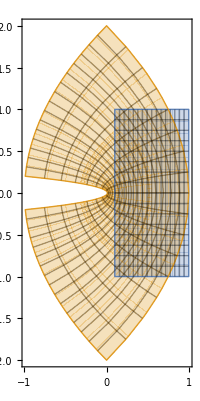

```mathematica
f[z_]:=z^2
ParametricPlot[{
ReIm[x + I y],
ReIm[f[x + I y]]
},
{x,0.1,1},
{y, -1,1},
Mesh->Automatic,
PlotRange->All]
```

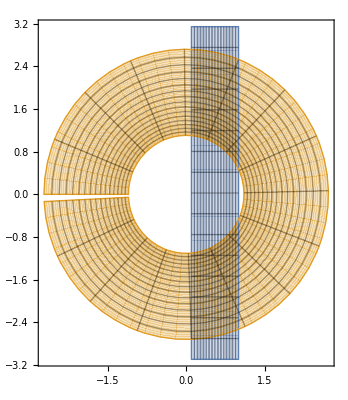

```mathematica
f[z_]:=E^z
ParametricPlot[{
ReIm[x + I y],
ReIm[f[x + I y]]
},
{x,0.1,1},
{y, -π+0.05,π},
Mesh->Automatic,
PlotRange->All]
```

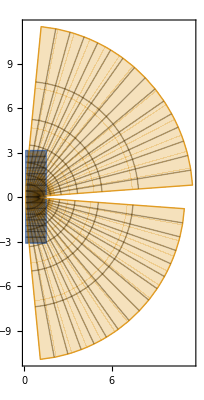

```mathematica
f[z_]:=Sin[z]
ParametricPlot[{
ReIm[x + I y],
ReIm[f[x + I y]]
},
{x,0.1,1.5},
{y, -π+0.05,π},
Mesh->Automatic,
PlotRange->All]
```

## Bilinear/Mobius Mappings

### Definition and Visualization

```mathematica
Mob[{a_,b_,c_,d_}][z_]:= (a z + b)/(c z +d)
{a,b,c,d}={1.2+3ⅈ, 0.1 ⅈ, 5-3.2 ⅈ, 1.2 -2 ⅈ};
(*Print["disc = ",a d - b c];*)
{R,cent}={1.2, 0.1 + ⅈ};
TabView[{
"Par x-y"->ParametricPlot[
ReIm[Mob[{a,b,c,d}][x+ⅈ y]],
{x, -12,12},
{y,-12,12},
Mesh->Automatic,
BoundaryStyle->Red],
"CPlot"->ComplexPlot3D[Mob[{a,b,c,d}][z],{z,2},
Mesh->Automatic],
"Par Circle"->ParametricPlot[{
ReIm[R ⅇ^(ⅈ θ)+cent],
ReIm[Mob[{a,b,c,d}][R ⅇ^(ⅈ θ)+cent]]
},
{θ,0, 2π},
PlotRange->All]
}]
```

123

```mathematica
123
```

### 3 Points to 3 Points

There is a unique bilinear map satisfying
	z_1→w_1
	z_2→w_2
	z_3→w_3
Maps circles and lines (clines) to circles and lines!

```mathematica
Clear[a,b,c,d]
{{z1,z2,z3},{w1,w2,w3}}=RandomComplex[{-1-I,1+I},{2,3}];
Solve[{
(a z1 +b)/(c z1+ d)==w1,
(a z2 +b)/(c z2+ d)==w2,
(a z3 +b)/(c z3+ d)==w3

},{a,b,c,d}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→(-0.611552+0.0278291 ⅈ) a,c→(1.26241-0.126555 ⅈ) a,d→(-0.02563+0.899099 ⅈ) a}}

How should I make sure this works as claimed? 
How would you do this by hand?
How do you know it always works?
…

### Real Axis to Unit Circle

The simplest line in ℂ is probably the real axis.  The simplest 3 points on the real axis are probably -1,0,1.   The simplest circle in ℂ is probably the unit circle.  The simplest 3 points on the unit circle are probably -1,ⅈ,1

```mathematica
Clear[a,b,c,d,Mob]
Mob[{a_,b_,c_,d_}][z_]:= (a z + b)/(c z +d)
InvMob[{a_,b_,c_,d_}][z_]:= Mob[{d,-b,-c,a}][z]
{{z1,z2,z3},{w1,w2,w3}}={{-1,0,1},{-1,ⅈ,1}};
Solve[{
(a z1 +b)/(c z1+ d)==w1,
(a z2 +b)/(c z2+ d)==w2,
(a z3 +b)/(c z3+ d)==w3

},{a,b,c,d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→ⅈ a,c→ⅈ a,d→a}}

```mathematica
RToUC[z_]:=Mob[{1,I,I,1}][z]
UCToR[z_]:=InvMob[{1,I,I,1}][z]
TabView[{
"RToUC"->ParametricPlot[ReIm[RToUC[x]],{x,-1,1},PlotRange->1.2{{-1,1},{-1,1}}],
"UCToR"->ParametricPlot[ReIm[UCToR[E^(I θ)]],{θ,0,π},PlotRange->1.2{{-1,1},{-1,1}}],
"RToUC"->ParametricPlot[{
ReIm[x+I y],
ReIm[RToUC[x+I y]]
},{x,-1,1},{y,-0.1,0.1},PlotRange->1.2{{-1,1},{-1,1}},Mesh->Automatic],
"UCToR"->ParametricPlot[{
ReIm[r E^(I θ)],
ReIm[UCToR[r E^(I θ)]]},{θ,0,π},{r,0.9,1.1},PlotRange->1.2{{-1,1},{-1,1}},Mesh->Automatic]
}]
```

1234

### What are Mobius Transforms good for? Absolutely Nothing! Designing and building Conformal Maps!

## Infinite Sums

∑_(n=1)^∞ 1/(n^2+1)

```mathematica
Sum[ 1/(n^2+1),{n,1,∞}]
```

1/2 (-1+π Coth[π])

```mathematica
∑_(n=-∞)^∞ 1/(n^2+1)
```

```mathematica
1+Sum[ 1/((-n)^2+1),{n,1,∞}]+Sum[ 1/(n^2+1),{n,1,∞}]
```

π Coth[π]

```mathematica
Clear[z]
ComplexPlot3D[ π Cot[π z],{z, 3}]
```

-Graphics3D-

```mathematica
Sum[ 1/((n+1/2)^2+a^2),{n,-∞,∞}]
```

(π Tanh[a π])/a

## Stuff

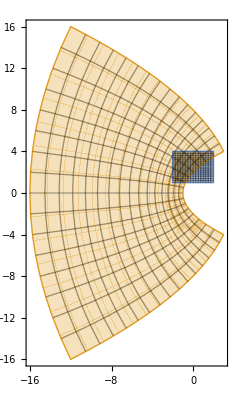

```mathematica
f[z_]:= z^2
ParametricPlot[{
 ReIm[ x + I y],
ReIm[ f[x + I y]]},{x, -2,2},{y, 1, 4},
Mesh->Automatic]
```

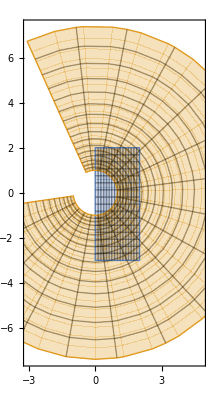

```mathematica
f[z_]:= E^z
ParametricPlot[{
 ReIm[ x + I y],
ReIm[ f[x + I y]]},{x, 0,2},{y, -3, 2},
Mesh->Automatic]
```

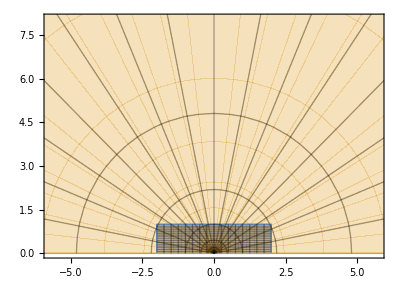

```mathematica
f[z_]:= E^(π z)
ParametricPlot[{
 ReIm[ x + I y],
ReIm[ f[x + I y]]},{x, -2,2},{y, 0, 1},
Mesh->Automatic]
```

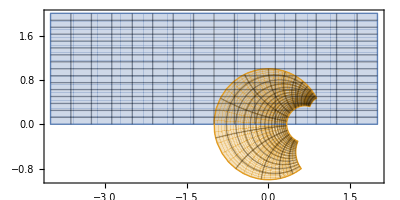

```mathematica
f[z_]:= (z-ⅈ)/(z+ⅈ)
ParametricPlot[{
 ReIm[ x + I y],
ReIm[ f[x + I y]]},{x, -4,2},{y, 0, 2},
Mesh->Automatic]
```

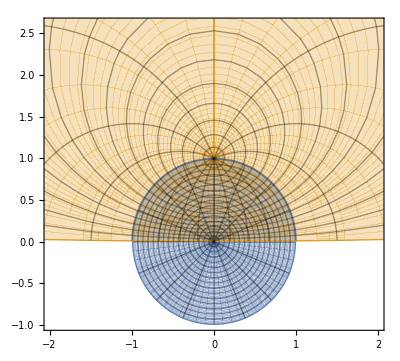

```mathematica
f[w_]:= ⅈ (1+w)/(1-w)
ParametricPlot[{
 ReIm[ r E^(ⅈ θ)],
ReIm[ f[r E^(ⅈ θ)]]},{r,0,0.99},{θ, 0, 2 π},
Mesh->Automatic]
```

```mathematica
f[z_]:=JacobiSN[z, I]
ComplexPlot3D[f[z],{z, 4}]
```

-Graphics3D-

```mathematica
f[z_]:=JacobiSN[z, 1+I]
ComplexPlot3D[f[z],{z, 4}]
```

-Graphics3D-

```mathematica
?JacobiSN
```